# Constructions for cographs and endographs of finite functions

## Introduction

This Mathematica notebook is licensed under a  .

It provides examples of  cographs and endographs of functions on finite sets.  

The notebook is still rough and incomplete.  It will be revised from time to time.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

Charles Wells

Utilities

```mathematica
Options[op]={Background->White,FontFamily->"Arial",FontWeight->Bold,FontSlant->Plain}
```

{Background→GrayLevel[1],FontFamily→Arial,FontWeight→Bold,FontSlant→Plain}

```mathematica
op[x_,loc_]:=Text[Style[x,14,Bold,Background->White],loc]
```

```mathematica
op["x",{0,1}]
```

Text[x,{0,1}]

## Making endographs

```mathematica
MakeFunctionRule[f_,n_]:=#->f[#]&/@ Table[k,{k,0,n-1}]
```

```mathematica
MakeRule[f_,l_]:=#->f[#]&/@l
```

```mathematica
Endograph[rule_,size_]:=GraphPlot[rule,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.2(200/size)]&),PlotStyle->Directive[Arrowheads[Small]],VertexRenderingFunction->(op[#2,#1]&),ImageSize->size]
```

```mathematica
Endograph[rule_,size_,vtc_]:=GraphPlot[rule,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.25(200/size)]&),PlotStyle->Directive[Arrowheads[Small]],
VertexCoordinateRules->vtc,VertexRenderingFunction->(op[#2,#1]&),ImageSize->size]
```

```mathematica
Endograph[rule_,size_,vtc_,gap_]:=GraphPlot[rule,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,gap]&),PlotStyle->Directive[Arrowheads[Small]],
VertexCoordinateRules->vtc,VertexRenderingFunction->(op[#2,#1]&),ImageSize->size]
```

## Making cographs

Basic example

This example will be used for testing the constructions. Names with lowercase are just for this example.  Names beginning with uppercase are permanent tools for the construction of the main function, Cograph.

```mathematica
f[a]:=c;f[b]:=a;f[c]:=c;f[d]:=b;f[e]:=d
```

```mathematica
BEsourcelist:={a,b,c,d,e};BEtargetlist:={a,b,c,d}
```

This particular choice of locations produces a column of addresses.

```mathematica
BEsourcelocs:={{1,5},{1,4},{1,3},{1,2},{1,1}}
```

```mathematica
BEtargetlocs:={{2,4.4},{2,3.5},{2,2.5},{2,1.5}}
```

Other possibilities, such as rows, may also be suitable:

```mathematica
BErowsourcelocs:={{1,1},{2,1},{3,1},{4,1},{5,1}}
```

```mathematica
BErowtargetlocs:={{1.5,0},{2.5,0},{3.5,0},{4.5,0}}
```

Preliminary functions

## SetLocs

SetLocs associates each source and target element with a location

```mathematica
SetLocs[source_,locs_]:={source,locs}//Transpose
```

sourceplacement attaches elements of the sourcelist to locations in sourcelocs in the order they occur in each list. By writing out the placement functions by hand you can arrange them in any way you want.

### Applied to Basic Example

```mathematica
sourceplacement:=SetLocs[BEsourcelist,BEsourcelocs]
```

```mathematica
sourceplacement
```

{{a,{1,5}},{b,{1,4}},{c,{1,3}},{d,{1,2}},{e,{1,1}}}

```mathematica
targetplacement:=SetLocs[BEtargetlist,BEtargetlocs]
```

```mathematica
targetplacement
```

{{a,{2,4.4}},{b,{2,3.5}},{c,{2,2.5}},{d,{2,1.5}}}

## DisplayNodes

DisplayNodes formats the nodes, resulting in a list which Graphics uses to display them.

```mathematica
DisplayNodes[list_,locs_]:=MapThread[op,{list,locs}]
```

### Applied to Basic Example

```mathematica
sourcecol:=DisplayNodes[BEsourcelist,BEsourcelocs]
```

```mathematica
sourcecol
```

{Text[a,{1,5}],Text[b,{1,4}],Text[c,{1,3}],Text[d,{1,2}],Text[e,{1,1}]}

```mathematica
targetcol:=DisplayNodes[BEtargetlist,BEtargetlocs]
```

```mathematica
targetcol
```

{Text[a,{2,4.4}],Text[b,{2,3.5}],Text[c,{2,2.5}],Text[d,{2,1.5}]}

```mathematica
Show[
Graphics[Flatten[{{sourcecol},{targetcol}}],
ImageSize->50,AspectRatio->3]]
```

-Graphics-

## ArrowSourceLoc and ArrowTargetLoc

```mathematica
arrowsource[chr_,slist_]:=Position[slist,chr][[1]][[1]]
```

```mathematica
ArrowSourceLoc[chr_,slist_,slocs_]:=slocs[[arrowsource[chr,slist]]]
```

```mathematica
arrowtarget[chr_,func_,slist_,tlist_]:=Position[tlist,func[chr]][[1]][[1]]
```

```mathematica
ArrowTargetLoc[chr_,func_,slist_,tlist_,tlocs_]:=tlocs[[arrowtarget[chr,func,slist,tlist]]]
```

### Applied to Basic Example

```mathematica
ArrowTargetLoc[a,f,BEsourcelist,BEtargetlist,BEtargetlocs]
```

{2,2.5}

```mathematica
f[a]:=c;f[b]:=a;f[c]:=c;f[d]:=b;f[e]:=d (*unevaluated reminder of our example function*)
```

```mathematica
BEsourcelocs:={{1,5},{1,4},{1,3},{1,2},{1,1}}
```

```mathematica
BEtargetlocs:={{2,4},{2,3},{2,2},{2,1}}
```

## ArrowList

```mathematica
ArrowList[func_,slist_,tlist_,slocs_,tlocs_,gap_]:=
Arrow[{ArrowSourceLoc[#,slist,slocs],ArrowTargetLoc[#,func,slist,tlist,tlocs]},gap]&/@slist
```

### Applied to Basic Example

```mathematica
ArrowList[f,BEsourcelist,BEtargetlist,BEsourcelocs,BEtargetlocs,.03]
```

{Arrow[{{1,5},{2,2.5}},0.03],Arrow[{{1,4},{2,4.4}},0.03],Arrow[{{1,3},{2,2.5}},0.03],Arrow[{{1,2},{2,3.5}},0.03],Arrow[{{1,1},{2,1.5}},0.03]}

Definition of Cograph

```mathematica
Cograph[func_,slist_,tlist_,slocs_,tlocs_,gap_]:=
Graphics[{Arrowheads->Small,DisplayNodes[slist,slocs] ~Join~DisplayNodes[tlist,tlocs]~Join~ArrowList[func,slist,tlist,slocs,tlocs,gap]}]
```

### Cograph of the Basic Example

```mathematica
Show[
Cograph[f,BEsourcelist,BEtargetlist,BErowsourcelocs,BErowtargetlocs,Scaled[.0005]],ImageSize->100,AspectRatio->.5]
```

-Graphics-

```mathematica
Show[
Cograph[f,BEsourcelist,BEtargetlist,BEsourcelocs,BEtargetlocs,Scaled[.0005]],ImageSize->50,AspectRatio->3]
```

-Graphics-

### Alternative ordering

An alternative ordering of the nodes makes a clearer picture of how the function behaves. Note that the sourcelocs and targetlocs are the same.

```mathematica
f2[a]:=c;f2[b]:=a;f2[c]:=c;f2[d]:=b;f2[e]:=d
```

```mathematica
sourcelist2:={c,a,b,d,e};targetlist2:={c,a,b,d}
```

```mathematica
Show[
Cograph[f2,sourcelist2,targetlist2,BEsourcelocs,BEtargetlocs,Scaled[.0005]],ImageSize->50,AspectRatio->3]
```

-Graphics-

### Horizontal cograph

```mathematica
rearrcograph:=Show[
Cograph[f2,sourcelist2,targetlist2,{{5,1},{4,1},{3,1},{2,1},{1,1}},{{4.5,0},{3.5,0},{2.5,0},{1.5,0}},Scaled[.0007]],ImageSize->150,AspectRatio->.3]
```

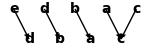

```mathematica
rearrcograph
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\rearrcograph.png",rearrcograph];
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\rearrcograph.gif",rearrcograph];
```

```mathematica
Export["rearrcograph.png",rearrcograph];
```

```mathematica
Export["rearrcograph.gif",rearrcograph];
```

An endograph showing the same example

```mathematica
MakeFunctionRule[f_,n_]:=#->f[#]&/@ Table[k,{k,0,n-1}]
```

```mathematica
MakeRule[f_,l_]:=#->f[#]&/@l
```

```mathematica
MakeRule[f2,{c,a,b,d,e}]
```

{c→c,a→c,b→a,d→b,e→d}

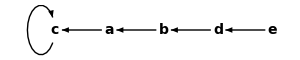

```mathematica
Endograph[{c->c,a->c,b->a,d->b,e->d},300]
```

## Examples

Example 1

```mathematica
Remove[f,f1,g]
```

## Endographs of g

```mathematica
g[n_]:=Mod[n^2+1,11]
```

```mathematica
g[#]&/@{0,1,2,3,4,5,6,7,8,9,10,11,12}
```

{1,2,5,10,6,4,4,6,10,5,2,1,2}

```mathematica
MakeFunctionRule[g,13]
```

{0→1,1→2,2→5,3→10,4→6,5→4,6→4,7→6,8→10,9→5,10→2,11→1,12→2}

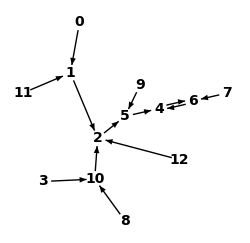

```mathematica
Endograph[MakeFunctionRule[g,13],250]
```

```mathematica
lyout={6->{1,0},7->{0,0},4->{2,0},5->{3,0},9->{3,1},2->{4,0},10->{5,-.66},3->{6,-.33},8->{6,-1.33},1->{5,.66},0->{6,1.33},11->{6,.33},12->{4,1}};
```

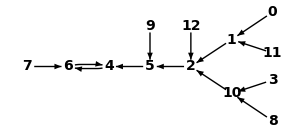

```mathematica
Endograph[MakeFunctionRule[g,13],300,lyout]
```

## Cographs of g

```mathematica
mod12list={0,1,2,3,4,5,6,7,8,9,10,11,12}
```

{0,1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
sourcelocsEx1:={0,#}&/@mod12list//Reverse
```

```mathematica
sourcelocsEx1
```

{{0,12},{0,11},{0,10},{0,9},{0,8},{0,7},{0,6},{0,5},{0,4},{0,3},{0,2},{0,1},{0,0}}

```mathematica
targetlocsEx1:={1,#}&/@mod12list//Reverse
```

```mathematica
targetlocsEx1
```

{{1,12},{1,11},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1},{1,0}}

```mathematica
g[8]
```

10

```mathematica
Show[
Cograph[g,{0,1,2,3,4,5,6,7,8,9,10,11,12},{0,1,2,3,4,5,6,7,8,9,10,11,12},{{0,12},{0,11},{0,10},{0,9},{0,8},{0,7},{0,6},{0,5},{0,4},{0,3},{0,2},{0,1},{0,0}},{{1,12},{1,11},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1},{1,0}},
Scaled[.0009]],ImageSize->70,AspectRatio->6]
```

-Graphics-

### Horizontal cograph

```mathematica
{1,#}&/@mod12list
```

{{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12}}

```mathematica
{0,#}&/@mod12list
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{0,11},{0,12}}

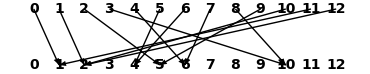

```mathematica
Show[
Cograph[g,mod12list,mod12list,{{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1}},{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0}},
Scaled[.0009]],ImageSize->370,AspectRatio->.2]
```

### Cograph of g with rearranged domain

```mathematica
Show[
Cograph[g,{7,6,4,5,9,2,12,10,1,8,3,0,11},{7,6,4,5,9,2,12,10,1,8,3,0,11},{{0,12},{0,11},{0,10},{0,9},{0,8},{0,7},{0,6},{0,5},{0,4},{0,3},{0,2},{0,1},{0,0}},{{1,12},{1,11},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1},{1,0}},
Scaled[.0009]],ImageSize->70,AspectRatio->6]
```

-Graphics-

### Horizontal rearranged cograph

```mathematica
{#,0}&/@mod12list
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0}}

```mathematica
{#,1}&/@mod12list
```

{{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1}}

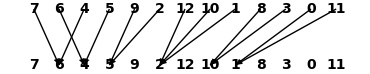

```mathematica
Show[
Cograph[g,{7,6,4,5,9,2,12,10,1,8,3,0,11},{7,6,4,5,9,2,12,10,1,8,3,0,11},{{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1}},{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0}},
Scaled[.0005]],ImageSize->370,AspectRatio->.2]
```

Example 2: A permutation

```mathematica
Remove[g,h,p]
```

```mathematica
p[0]:=0;p[1]:=2;p[2]:=1;p[3]:=4;p[4]:=5;p[5]:=3;p[6]:=7;p[7]:=8;p[8]:=9;p[9]:=6;
```

```mathematica
MakeFunctionRule[p,10]
```

{0→0,1→2,2→1,3→4,4→5,5→3,6→7,7→8,8→9,9→6}

## Endograph

```mathematica
endographperm:=Endograph[{0->0,1->2,2->1,3->4,4->5,5->3,6->7,7->8,8->9,9->6},180]
```

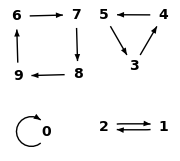

```mathematica
endographperm
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\endographperm.png",endographperm]
```

W:\www\MM\Mathematica\Function Representations\endographperm.png

## Cograph

```mathematica
{#,1}&/@{1,2,3,4,5,6,7,8,9,10}
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}}

```mathematica
{#,0}&/@{1,2,3,4,5,6,7,8,9,10}
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

```mathematica
cographperm:=Show[
Cograph[p,{0,1,2,3,4,5,6,7,8,9},{0,1,2,3,4,5,6,7,8,9},{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}},{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}},
Scaled[.0006]],ImageSize->300,AspectRatio->.2]
```

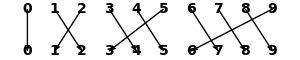

```mathematica
cographperm
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\cographperm.png",cographperm]
```

W:\www\MM\Mathematica\Function Representations\cographperm.png

Example 3

```mathematica
Remove[p]
```

```mathematica
h[0]:=2;h[1]:=2;h[2]:=3;h[3]:=3;h[4]:=15;h[5]:=7;h[6]:=7;h[7]:=15;h[8]:=16;h[9]:=10;h[10]:=14;h[11]:=13;h[12]:=14;h[13]:=14;h[14]:=17;h[15]:=16;h[16]:=17;h[17]:=15
```

## Endograph

```mathematica
hrule=MakeFunctionRule[h,18]
```

{0→2,1→2,2→3,3→3,4→15,5→7,6→7,7→15,8→16,9→10,10→14,11→13,12→14,13→14,14→17,15→16,16→17,17→15}

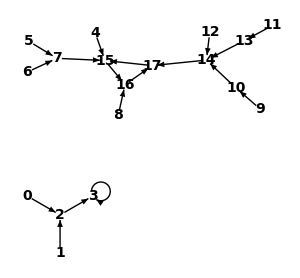

```mathematica
Endograph[hrule,300]
```

```mathematica
hlayout={3->{-.3,-1},2->{-.3,0},0->{-.8,1},1->{.3,1},5->{1,.6},6->{1,-.6},7->{2,0},15->{3,0},4->{3,1},16->{3.5,-1},8->{3.5,-2},17->{4,0},14->{5,0},12->{5,1},13->{6,.6},10->{6,-.7},9->{7,-1.6},11->{7,1.3}};
```

```mathematica
bigendo:=Endograph[hrule,300,hlayout]
```

```mathematica
Export["W:\\www\\MM\Mathematica\\Function Representations\\bigendo.png",bigendo]
```

W:\www\MM\Mathematica\Function Representations\bigendo.png

## Cograph

### Not rearranged

```mathematica
{#,1}&/@Table[i,{i,0,17}]
```

{{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1}}

```mathematica
{#,0}&/@Table[i,{i,0,17}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0}}

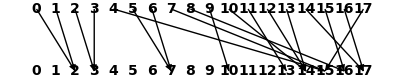

```mathematica
Show[
Cograph[h,Table[i,{i,0,17}],Table[i,{i,0,17}],{#,1}&/@Table[i,{i,0,17}],{#,0}&/@Table[i,{i,0,17}],
Scaled[.0010]],ImageSize->400,AspectRatio->.2]
```

### Rearranged

```mathematica
h[0]:=2;h[1]:=2;h[2]:=3;h[3]:=3;h[4]:=15;h[5]:=7;h[6]:=7;h[7]:=15;h[8]:=16;h[9]:=10;h[10]:=14;h[11]:=13;h[12]:=14;h[13]:=14;h[14]:=17;h[15]:=16;h[16]:=17;h[17]:=15
```

```mathematica
hdomrearr={0,1,2,3,5,6,7,4,8,15,16,17,14,10,12,13,9,11};
```

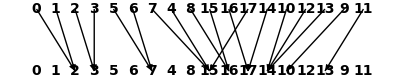

```mathematica
Show[
Cograph[h,hdomrearr,hdomrearr,{#,1}&/@Table[i,{i,0,17}],{#,0}&/@Table[i,{i,0,17}],
Scaled[.0010]],ImageSize->400,AspectRatio->.2]
```

Example 4

```mathematica
Remove[h]
```

## Endograph

```mathematica
newrule:={0->2,1->2,2->3,3->4,4->3,5->4,6->3,7->5,8->16,9->16,10->14,11->13,12->15,13->14,14->17,15->16,16->17,17->15}
```

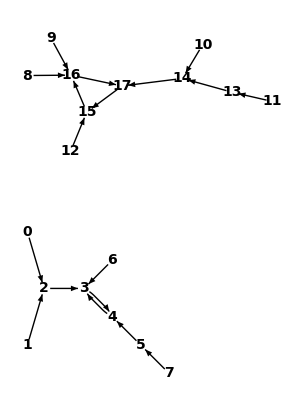

```mathematica
Endograph[newrule,300]
```

```mathematica
newlayout={0->{0,-.3},1->{0,.3},2->{1,0},3->{2,0},4->{3,0},5->{4,0},6->{2,1},7->{5,0},8->{0.5,-2},9->{2.5,-2},10->{4,-1.6},11->{5,-1},12->{0,-1},13->{4,-1},14->{3,-1},15->{1,-1},16->{1.5,-2},17->{2,-1}}
```

{0→{0,-0.3},1→{0,0.3},2→{1,0},3→{2,0},4→{3,0},5→{4,0},6→{2,1},7→{5,0},8→{0.5,-2},9→{2.5,-2},10→{4,-1.6},11→{5,-1},12→{0,-1},13→{4,-1},14→{3,-1},15→{1,-1},16→{1.5,-2},17→{2,-1}}

```mathematica
bigendo2:=Endograph[newrule,390,newlayout,Scaled[.0008]]
```

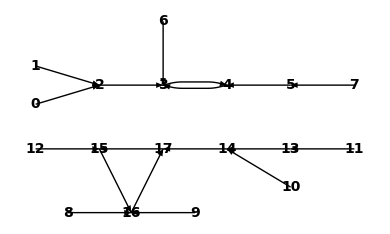

```mathematica
bigendo2
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\bigendo.png",bigendo2]
```

W:\www\MM\Mathematica\Function Representations\bigendo.png

Example 5 : a tree

```mathematica
t[1]:=4;t[2]:=4;t[3]:=6;t[4]:=4;t[5]:=2;t[6]:=4;t[7]:=2;t[8]:=7;t[9]:=7;t[0]:=6
```

## Endograph

```mathematica
trule=MakeFunctionRule[t,10]
```

{0→6,1→4,2→4,3→6,4→4,5→2,6→4,7→2,8→7,9→7}

```mathematica
treeex:=Endograph[trule,280]
```

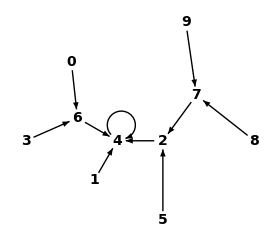

```mathematica
treeex
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\treeex.png",treeex]
```

W:\www\MM\Mathematica\Function Representations\treeex.png

## Cograph

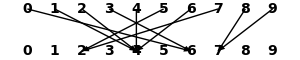

```mathematica
Show[
Cograph[t,Table[i,{i,0,9}],Table[i,{i,0,9}],{#,1}&/@Table[i,{i,0,9}],{#,0}&/@Table[i,{i,0,9}],
Scaled[.0010]],ImageSize->300,AspectRatio->.2]
```

```mathematica
tdomrearr={9,8,7,5,2,4,1,6,0,3};
```

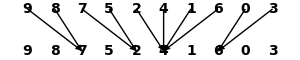

```mathematica
Show[
Cograph[t,tdomrearr,tdomrearr,{#,1}&/@Table[i,{i,0,9}],{#,0}&/@Table[i,{i,0,9}],
Scaled[.0010]],ImageSize->300,AspectRatio->.2]
```

Example 6

For any endofunction of a finite field of order q,  x^(q-2) is a permutation.

```mathematica
xp[n_]:=Mod[n^15,17]
```

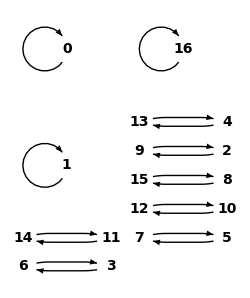

```mathematica
Endograph[MakeFunctionRule[xp,17],250]
```

```mathematica
xp2[n_]:=Mod[n^15+5n^14-n^10,17]
```

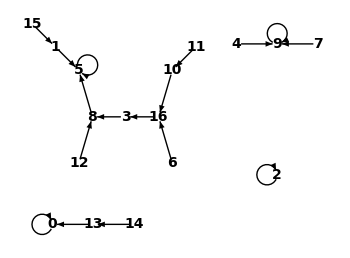

```mathematica
Endograph[MakeFunctionRule[xp2,17],350]
```

```mathematica
xp3[n_]:=Mod[n^14,17]
```

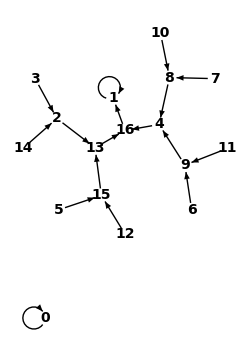

```mathematica
Endograph[MakeFunctionRule[xp3,17],250]
```

```mathematica
xp4[n_]:=Mod[n^14+10,17]
```

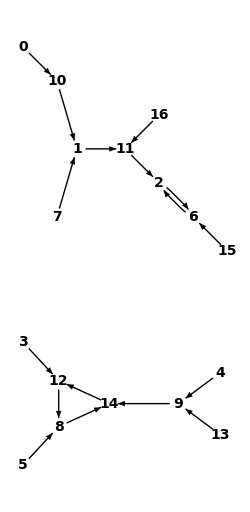

```mathematica
Endograph[MakeFunctionRule[xp4,17],250]
```

```mathematica
xp5[n_]:=Mod[6n+5,17]
```

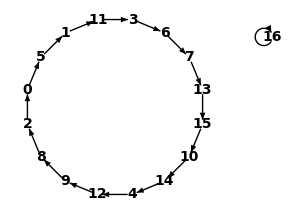

```mathematica
Endograph[MakeFunctionRule[xp5,17],300]
```

```mathematica
xp6[n_]:=Mod[6n^2+5,17]
```

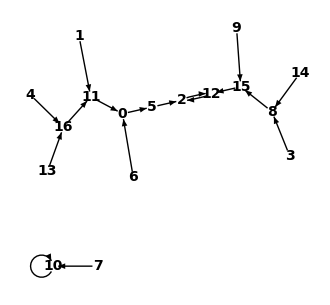

```mathematica
Endograph[MakeFunctionRule[xp6,17],330]
```

Other notations

## Table

```mathematica
tableop[x_]:=Style[x,16]
```

```mathematica
grid1:=Show[
Graphics[{Text[Grid[{{tableop[a],tableop[c]},{tableop[b],tableop[a]},{tableop[c],tableop[c]},{tableop[d],tableop[b]},{tableop[e],tableop[d]}},Frame->All],{0,0}]
}
],ImageSize->80]
```

```mathematica
grid1
```

-Graphics-

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\grid1.png",grid1]
```

W:\www\MM\Mathematica\Function Representations\grid1.png

```mathematica
grid2:=
Text[Grid[{{tableop["Albert Singlestone"],tableop["Personnel"]},{tableop["Eva Peron"],tableop["Information Services"]},{tableop["Minnie Tonka"],tableop["Head Office"]},{tableop["Theodore Rosefield"],tableop["Personnel"]},{tableop["Roy Roget"],tableop["Head Office"]}},Alignment->Left,Frame->All]]
```

```mathematica
grid2
```

Albert Singlestone | Personnel
Eva Peron | Information Services
Minnie Tonka | Head Office
Theodore Rosefield | Personnel
Roy Roget | Head Office

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\grid2.png",grid2]
```

W:\www\MM\Mathematica\Function Representations\grid2.png

```mathematica
"W:\\www\\MM\\Mathematica\\Function Representations\\grid2.png"
```

W:\www\MM\Mathematica\Function Representations\grid2.png

```mathematica
{320,200}1.1
```

{352.,220.}